# Simulating correlated random walk using von Mises-Fisher distribution Feb 2019 - Oct 2020 - Dec 2020

### Correlated random walk: varying k_t (average turning angle) and sampling frequency

This is the main function defining random vector relative to vector μ with a bias defined by the concentration parameter κ

```mathematica
vonMisesFisherRandom[μ_?VectorQ,κ_?NumericQ]:=Module[{ξ=RandomReal[],w},w=1+(Log[ξ]+Log[1+(1-ξ) Exp[-2 κ]/ξ])/κ;
RotationTransform[{{0,0,1},Normalize[μ]}][Append[Sqrt[1-w^2] Normalize[RandomVariate[NormalDistribution[],2]],w]]]
```

```mathematica
(* Example of one random vector *)

SeedRandom[1]
rmean=2;
alpha=5.5;
xmin=rmean*(alpha-1)/alpha;
mu0=N[{1,0,0}]
x10={0,0,0};
x20={1,0,0};
mu=RandomVariate[ParetoDistribution[xmin,alpha]]*vonMisesFisherRandom[mu0,0.0001]
VectorAngle[mu0,mu]/Pi*180
```

{1.,0.,0.}

{-1.31917,0.987722,-0.406926}

141.

Function OneMovement defining one movement with a correlated random walk with bias defined by kappaT and 2 cell positions x1 and x2 to define movement vector relate to which next movement will be done. Output of the function is the position x2 and the next position. Movement length is randomly sampled from Pareto distribution with parameters xmin and alpha.

```mathematica
Clear[kappaT,OneMovement];
OneMovement[{x1_,x2_}]:={x2,x2+RandomVariate[ParetoDistribution[xmin,alpha]]*vonMisesFisherRandom[x2-x1,kappaT]}
kappaT=1.0001;
x10={0,0,0};
x20={1,0,0};
OneMovement[{x10,x20}]
```

{{1,0,0},{2.35611,-1.38238,0.0116663}}

```mathematica
(* calculating nsteps for one cell moving *)
SeedRandom[1];
nsteps=500;
onecellmovement=NestList[OneMovement,{x10,x20},nsteps];
Length[%]
```

501

```mathematica
(* taking sequential positions of the cell and plotting it *)
alldata2=onecellmovement[[All,2]];

xlim=50;
myFig1=Show[
ListPointPlot3D[alldata2,
AspectRatio->1,
Epilog->{
},
PlotRange->{{-xlim,xlim},{-xlim,xlim},{-xlim,xlim}}
]/.Point[a___]:>{Thick,Blue,Line[a]},
ListPointPlot3D[alldata2]
]
```

-Graphics3D-

99.2709-13.01 x

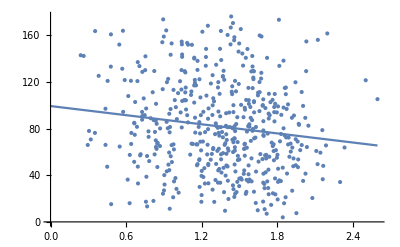

```mathematica
(* Calculating correlation between average turning angle and average speed per cell *)
k=3; (* sample every 3 positions - vary between 1 and 49 *)
tempdata1=Table[{EuclideanDistance[alldata2[[i+k]],alldata2[[i+2*k]]]/k,180*VectorAngle[alldata2[[i+k]]-alldata2[[i]],alldata2[[i+2*k]]-alldata2[[i+k]]]/(Pi)},{i,1,Length[alldata2]-2*k}];
f[x_]=Fit[tempdata1,{1,x},x]
Show[ListPlot[{tempdata1}],Plot[{f[x]},{x,0,Max[tempdata1[[All,1]]]}]]
```

```mathematica
(* simulating m cells with few movements: define kappa. Data are stored in alldata variable *)

SeedRandom[3]

kappaT=10;
nsteps=100; (* number of movements per cell *)
ncells=500; (* number of cells simulated *)
rmean=2; (*parameter of the Pareto distribution for step length movement *)
alpha=5.5;
xmin=rmean*(alpha-1)/alpha;

alldata=Table[
onecellmovement=NestList[OneMovement,{x10,x20},nsteps];
onecellmovement[[All,2]],{j,1,ncells}];
```

```mathematica
k=7;
tempdata1=Map[Table[{EuclideanDistance[#[[i+k]],#[[i+2*k]]]/k,180*VectorAngle[#[[i+k]]-#[[i]],#[[i+2*k]]-#[[i+k]]]/(Pi)},{i,1,Length[#]-2*k}]&,alldata];
tempdata2=Map[Mean[#]&,tempdata1];
```

135.416-49.0717 x

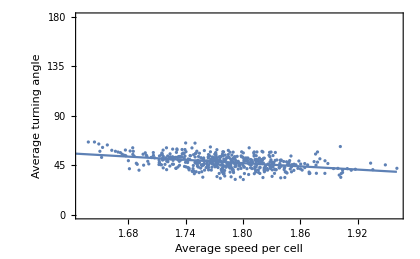

```mathematica
f[x_]=Fit[tempdata2,{1,x},x]
slope=f[x][[2,1]];
{vmean,phimean}=Mean[tempdata2];
Show[
ListPlot[{tempdata2},
PlotRange->{All,{0,180}},
Frame->True,
FrameTicks->{Automatic,Table[{i,i,{0.02,0}},{i,0,180,45}]},
FrameLabel->{"Average speed per cell","Average turning angle"},
Epilog->{
}
],
Plot[f[x],{x,0,Max[tempdata2[[All,1]]]}]
]
```